```mathematica
plus[{a_,b_},len_]:=Mod[a+b-1,len]+1
minus[{a_,b_},len_]:=Mod[a-b-1,len]+1
```

```mathematica
plus[a_,b_,len_]:=Mod[a+b-1,len]+1
minus[a_,b_,len_]:=Mod[a-b-1,len]+1
```

```mathematica
pic[sol_,len_,offset_:0]:=Module[{},
size=3;
Graphics[{Circle[{0,0},len+size],Circle[{0,0},len-size],Table[Line[{{(len-size)Cos[2Pi (i+1/2)/len+Pi/2],(len-size)Sin[2Pi (i+1/2)/len+Pi/2]},{(len+size) Cos[2Pi (i+1/2)/len+Pi/2],(len+size) Sin[2Pi (i+1/2)/len+Pi/2]}}],{i,1,len}],
Table[Text[Style[If[sol[[i]]>0,sol[[i]]," "],FontSize->12],{len Cos[2Pi plus[i,offset,len]/len+Pi/2],len Sin[2Pi plus[i,offset,len]/len+Pi/2]}],{i,1,len}]},ImageSize->8len]
]
```

```mathematica
unique[L_]:=Select[L,Count[L,#]==1&]
```

```mathematica
small:=Select[sols,First[Sort[{Rest[#],Reverse[Rest[#]]}]]==Rest[#]&]
```

```mathematica
f[n_,len_,offset_]:=Module[{},
sols={};
stack={{1}~Join~Table[0,{len-1}]};
While[Length[stack]>0,
top=First[stack];
stack=Rest[stack];
avail=Complement[Range[n],top];
taken=Select[Table[{i,top[[i]]},{i,1,len}],#[[2]]>0&];
occupied=Transpose[taken][[1]];
needed=Union[Complement[Map[plus[#,len]&,taken]~Join~Map[minus[#,len]&,taken],occupied]];
If[needed=={}&&avail=={},AppendTo[sols,top],
If[Length[needed]>0,
stack=stack~Join~Map[ReplacePart[top,needed[[1]]->#]&,avail],
stack=stack~Join~Map[ReplacePart[top,#->avail[[1]]]&,Complement[Range[len],occupied]]]]];
Map[Print[pic[#,len,offset-1]]&,Union[sols]];]
```

```mathematica
f[n_,len_]:=Module[{},
sols={};
stack={{1}~Join~Table[0,{len-1}]};
While[Length[stack]>0,
top=First[stack];
stack=Rest[stack];
avail=Complement[Range[n],top];
taken=Select[Table[{i,top[[i]]},{i,1,len}],#[[2]]>0&];
occupied=Transpose[taken][[1]];
needed=Union[Complement[Map[plus[#,len]&,taken]~Join~Map[minus[#,len]&,taken],occupied]];
If[needed=={}&&avail=={},AppendTo[sols,top],
If[Length[needed]>0,
stack=stack~Join~Map[ReplacePart[top,needed[[1]]->#]&,avail],
stack=stack~Join~Map[ReplacePart[top,#->avail[[1]]]&,Complement[Range[len],occupied]]]]];
sols=Union[sols];
Map[Print[pic[#,len,-1]]&,sols];]
```

```mathematica
f[n1_,n2_,len_]:=Module[{},(* other intervals *)
sols={};
stack={{n1}~Join~Table[0,{len-1}]};
While[Length[stack]>0,
top=First[stack];
stack=Rest[stack];
avail=Complement[Range[n1,n2],top];
taken=Select[Table[{i,top[[i]]},{i,1,len}],#[[2]]>0&];
occupied=Transpose[taken][[1]];
needed=Union[Complement[Map[plus[#,len]&,taken]~Join~Map[minus[#,len]&,taken],occupied]];
If[needed=={}&&avail=={},AppendTo[sols,top],
If[Length[needed]>0,
stack=stack~Join~Map[ReplacePart[top,needed[[1]]->#]&,avail],
stack=stack~Join~Map[ReplacePart[top,#->avail[[1]]]&,Complement[Range[len],occupied]]]]];
sols=Union[sols];
Map[Print[pic[#,len,-1]]&,sols];]
```

```mathematica
f[n_,len_]:=Module[{},
sols={};
stack={{1}~Join~Table[0,{len-1}]};
While[Length[stack]>0,
top=First[stack];
stack=Rest[stack];
avail=Complement[Range[n],top];
taken=Select[Table[{i,top[[i]]},{i,1,len}],#[[2]]>0&];
occupied=Transpose[taken][[1]];
needed=Union[Complement[Map[plus[#,len]&,taken]~Join~Map[minus[#,len]&,taken],occupied]];
If[needed=={}&&avail=={},AppendTo[sols,top],
If[Length[needed]>0,
stack=stack~Join~Map[ReplacePart[top,needed[[1]]->#]&,avail],
stack=stack~Join~Map[ReplacePart[top,#->avail[[1]]]&,Complement[Range[len],occupied]]]]];
sols=Union[sols];]
```

## size 4

```mathematica
n=9;
For[j=2,j≤n-1,j++,
For[k=12,k≤30,k=k+2,
Print[k];f[j,n,k]]]
```

## size 4

```mathematica
f[4,6,-1]
```

-Graphics-

-Graphics-

## size 5

```mathematica
f[5,7,2]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
f[5,8]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
f[5,11,6]
```

-Graphics-

-Graphics-

## size 6

```mathematica
f[6,10,1]
```

-Graphics-

-Graphics-

-Graphics-

«17 more identical outputs»

```mathematica
f[6,11]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
f[6,12,2]
```

-Graphics-

-Graphics-

```mathematica
f[6,13,7]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## size 7

```mathematica
f[7,12,3]
```

-Graphics-

-Graphics-

-Graphics-

«37 more identical outputs»

```mathematica
f[7,13,-4]
```

-Graphics-

-Graphics-

-Graphics-

«25 more identical outputs»

```mathematica
f[7,14,-1]
```

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

```mathematica
f[7,15,5]
```

-Graphics-

-Graphics-

## size 8

```mathematica
size=8;
cir=17;
For[n=1,n≤size-1,n++,
For[m=n+1,m≤size,m++,
c=Table[
pn=Position[sols[[j]],n][[1,1]];
pm=Position[sols[[j]],m][[1,1]];
minus[pn,pm,cir],{j,1,Length[sols]}];Print[n," ",m," ",c," ",unique[c]]]]
```

1 2 {16,16,16,2,15,1,3,2,2,3,14,1,15,1,14,15} {}

1 3 {14,14,4,16,16,3,15,5,1,13,2,3,12,13,4,1} {15,5,2,12}

1 4 {1,12,14,13,2,16,16,4,15,9,1,5,13,3,8,4} {12,14,2,15,9,5,3,8}

1 5 {4,11,9,4,1,13,12,16,16,5,5,6,1,8,12,13} {11,9,6,8}

1 6 {5,6,10,10,13,12,1,11,4,16,16,11,6,7,1,7} {5,13,12,4}

1 7 {11,1,7,9,6,6,5,1,11,10,12,16,16,10,7,8} {9,5,12,8}

1 8 {9,8,1,1,7,8,7,8,10,1,10,9,9,16,16,16} {}

2 3 {15,15,5,14,1,2,12,3,16,10,5,2,14,12,7,3} {1,16,10,7}

2 4 {2,13,15,11,4,15,13,2,13,6,4,4,15,2,11,6} {}

2 5 {5,12,10,2,3,12,9,14,14,2,8,5,3,7,15,15} {10,9,8,7}

2 6 {6,7,11,8,15,11,15,9,2,13,2,10,8,6,4,9} {7,13,10,4}

2 7 {12,2,8,7,8,5,2,16,9,7,15,15,1,9,10,10} {12,5,16,1}

2 8 {10,9,2,16,9,7,4,6,8,15,13,8,11,15,2,1} {10,16,7,4,6,13,11,1}

3 4 {4,15,10,14,3,13,1,16,14,13,16,2,1,7,4,3} {15,10,2,7}

3 5 {7,14,5,5,2,10,14,11,15,9,3,3,6,12,8,12} {7,2,10,11,15,9,6,8}

3 6 {8,9,6,11,14,9,3,6,3,3,14,8,11,11,14,6} {}

3 7 {14,4,3,10,7,3,7,13,10,14,10,13,4,14,3,7} {}

3 8 {12,11,14,2,8,5,9,3,9,5,8,6,14,3,12,15} {11,2,6,15}

4 5 {3,16,12,8,16,14,13,12,1,13,4,1,5,5,4,9} {3,8,14,9}

4 6 {4,11,13,14,11,13,2,7,6,7,15,6,10,4,10,3} {14,2,15,3}

4 7 {10,6,10,13,4,7,6,14,13,1,11,11,3,7,16,4} {14,1,3,16}

4 8 {8,13,4,5,5,9,8,4,12,9,9,4,13,13,8,12} {}

5 6 {1,12,1,6,12,16,6,12,5,11,11,5,5,16,6,11} {}

5 7 {7,7,15,5,5,10,10,2,12,5,7,10,15,2,12,12} {}

5 8 {5,14,9,14,6,12,12,9,11,13,5,3,8,8,4,3} {6,11,13,4}

6 7 {6,12,14,16,10,11,4,7,7,11,13,5,10,3,6,1} {12,14,16,4,13,5,3,1}

6 8 {4,2,8,8,11,13,6,14,6,2,11,15,3,9,15,9} {4,13,14,3}

7 8 {15,7,11,9,1,2,2,7,16,8,15,10,10,6,9,8} {11,1,16,6}

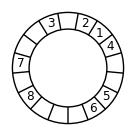

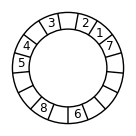

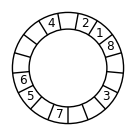

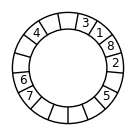

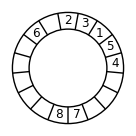

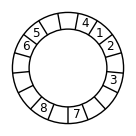

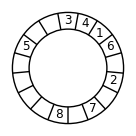

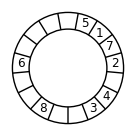

```mathematica
f[8,17,-2]
```

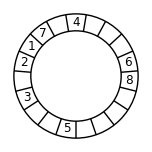

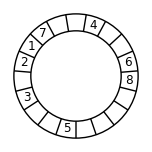

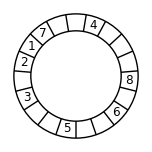

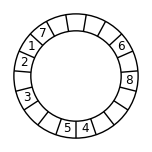

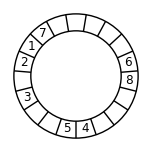

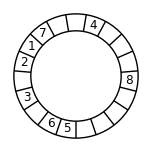

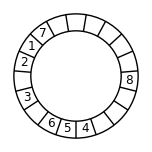

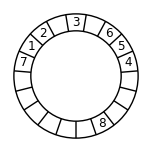

```mathematica
f[8,19,3]
```

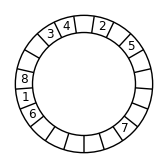

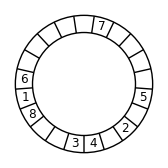

```mathematica
f[8,21,6]
```

## size 9

1 2 4 {1,7,6,0,0,0,0,0,8,0,0,9,0,0,0,0,5,0,2,0,4,3}

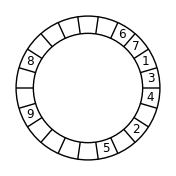

1 3 10 {1,2,0,9,0,0,0,0,0,8,0,0,3,0,0,6,7,5,0,0,0,4}

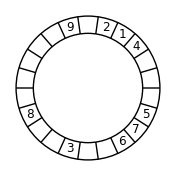

1 3 5 {1,5,0,0,0,0,8,0,9,0,0,0,0,0,6,0,0,3,4,0,2,7}

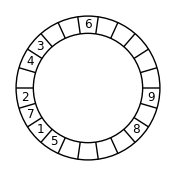

1 3 1 {1,7,6,0,0,0,0,0,8,0,0,9,0,0,0,0,5,0,2,0,4,3}

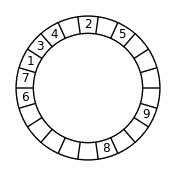

1 4 2 {1,7,6,0,0,0,0,0,8,0,0,9,0,0,0,0,5,0,2,0,4,3}

-Graphics-

1 4 8 {1,9,0,0,3,0,0,7,0,0,6,0,0,0,4,0,2,0,8,0,0,5}

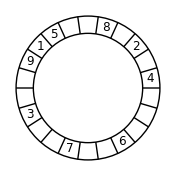

1 5 3 {1,4,3,0,0,8,0,7,0,0,0,0,0,6,9,0,0,0,0,5,0,2}

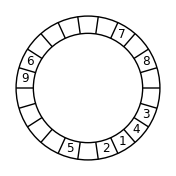

1 5 9 {1,8,0,0,0,0,0,0,7,9,0,0,0,5,0,6,0,0,3,4,0,2}

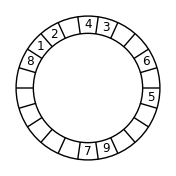

1 6 2 {1,3,4,0,2,0,5,0,0,0,0,9,0,0,8,0,0,0,0,0,6,7}

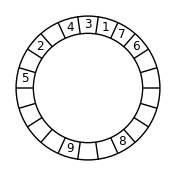

1 6 3 {1,4,0,3,0,5,7,0,0,0,9,0,0,8,0,0,0,0,0,6,0,2}

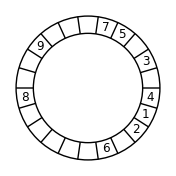

1 6 9 {1,4,3,0,0,8,0,7,0,0,0,0,0,6,9,0,0,0,0,5,0,2}

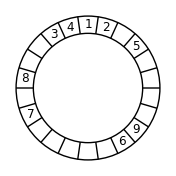

1 6 8 {1,5,0,0,0,0,8,0,9,0,0,0,0,0,6,0,0,3,4,0,2,7}

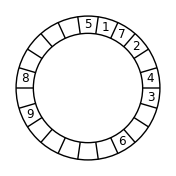

1 6 10 {1,5,0,0,8,0,2,0,4,0,0,0,6,0,0,7,0,0,3,0,0,9}

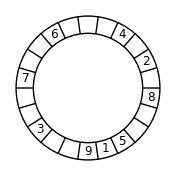

1 7 9 {1,2,0,3,0,0,6,0,0,0,0,0,9,7,0,0,0,5,0,0,8,4}

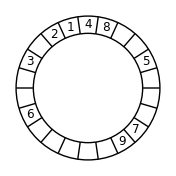

1 7 2 {1,4,0,0,0,5,0,0,0,0,9,0,0,8,0,0,6,0,0,3,7,2}

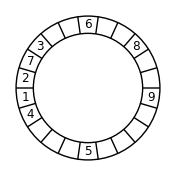

1 8 5 {1,2,0,5,0,0,0,0,9,6,0,0,0,0,0,7,0,8,0,0,3,4}

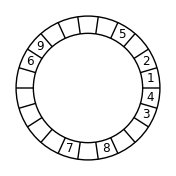

1 8 3 {1,4,3,0,0,5,0,0,0,0,9,6,0,0,0,0,0,7,0,8,0,2}

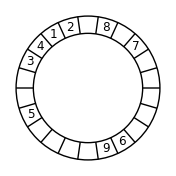

1 8 6 {1,7,2,0,4,3,0,0,6,0,0,0,0,0,9,0,8,0,0,0,0,5}

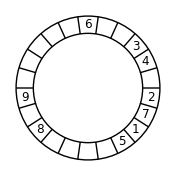

1 8 4 {1,9,0,0,3,0,0,7,0,0,6,0,0,0,4,0,2,0,8,0,0,5}

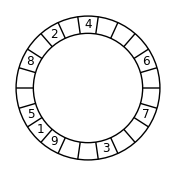

2 3 4 {1,2,0,6,0,0,0,0,0,8,0,0,9,0,0,0,7,5,0,3,0,4}

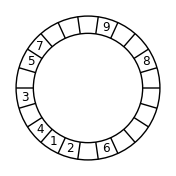

2 3 5 {1,7,2,0,4,0,0,0,8,0,9,0,0,0,0,0,6,0,0,3,0,5}

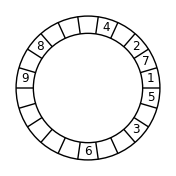

2 3 8 {1,7,3,0,0,5,0,0,8,0,2,0,4,0,0,0,6,0,0,0,0,9}

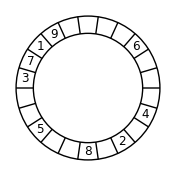

2 4 5 {1,2,0,3,0,0,6,0,0,0,0,0,9,0,8,0,0,5,4,0,0,7}

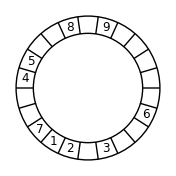

2 4 3 {1,8,0,0,0,0,0,0,0,9,0,0,0,0,5,6,7,0,4,3,0,2}

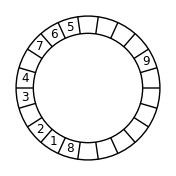

2 5 4 {1,7,0,0,0,0,0,0,8,0,9,0,4,0,0,0,6,5,0,3,0,2}

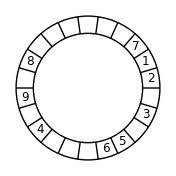

2 6 2 {1,4,0,3,0,5,7,0,0,0,9,0,0,8,0,0,0,0,0,6,0,2}

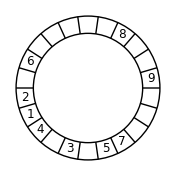

2 6 9 {1,7,0,0,0,6,0,0,8,0,0,3,4,0,2,0,5,0,0,0,0,9}

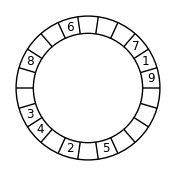

2 6 3 {1,9,0,0,0,6,5,0,2,0,4,3,0,0,8,0,0,0,0,0,0,7}

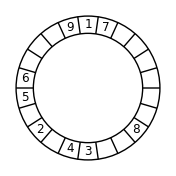

2 7 6 {1,4,0,0,0,5,0,0,8,0,9,0,0,0,0,7,6,0,0,3,0,2}

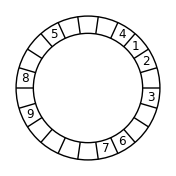

2 9 2 {1,4,0,0,0,5,7,6,0,0,3,0,0,8,0,0,0,0,0,9,0,2}

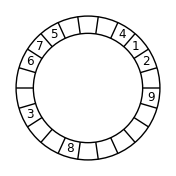

2 9 8 {1,5,0,3,0,0,6,0,0,0,0,0,9,0,8,0,0,0,4,0,2,7}

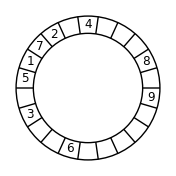

3 4 9 {1,4,0,0,0,5,7,6,0,0,3,0,0,8,0,0,0,0,0,9,0,2}

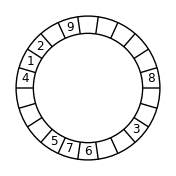

3 4 2 {1,4,0,3,0,5,7,0,0,0,9,0,0,8,0,0,0,0,0,6,0,2}

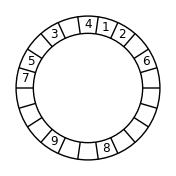

3 4 8 {1,7,0,0,0,0,0,0,8,0,2,0,4,0,0,0,6,5,0,0,3,9}

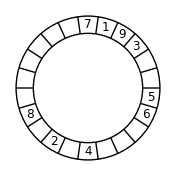

3 5 6 {1,7,2,0,4,3,0,0,6,0,0,0,0,0,9,0,8,0,0,0,0,5}

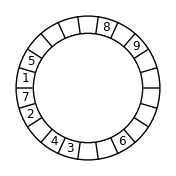

3 6 9 {1,2,0,8,0,7,0,0,0,0,0,6,9,0,0,0,0,5,0,0,3,4}

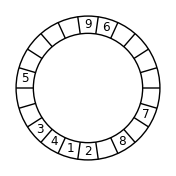

3 6 5 {1,7,0,0,0,0,6,0,8,0,0,3,4,0,2,0,5,0,0,0,0,9}

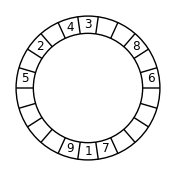

3 7 9 {1,2,0,3,0,0,6,0,0,8,0,0,9,0,0,0,7,5,0,0,0,4}

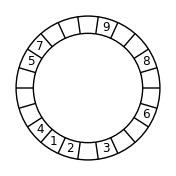

3 7 5 {1,2,0,5,0,0,0,0,9,6,0,0,0,0,0,7,0,8,0,0,3,4}

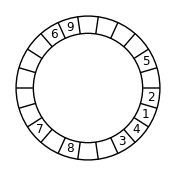

3 8 4 {1,2,0,3,4,0,7,6,5,0,0,0,0,9,0,0,0,0,0,0,0,8}

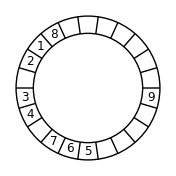

3 8 9 {1,3,4,0,2,0,5,0,0,0,0,9,0,0,8,0,0,0,0,0,6,7}

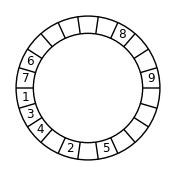

3 9 6 {1,2,0,3,0,0,5,0,0,0,7,8,0,0,0,0,0,6,0,9,0,4}

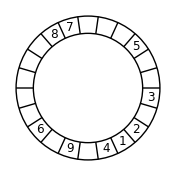

3 9 7 {1,2,0,6,0,0,0,0,0,8,0,0,9,0,0,0,7,5,0,3,0,4}

-Graphics-

3 9 1 {1,9,3,0,0,5,6,0,0,0,4,0,2,0,8,0,0,0,0,0,0,7}

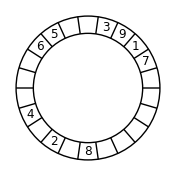

4 5 1 {1,2,0,3,0,0,6,0,0,0,0,0,9,0,8,0,0,5,4,0,0,7}

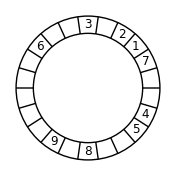

4 6 3 {1,8,0,0,0,0,0,0,0,9,0,0,0,0,5,6,7,0,4,3,0,2}

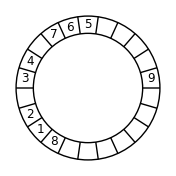

4 6 5 {1,9,0,0,0,6,5,0,2,0,4,3,0,0,8,0,0,0,0,0,0,7}

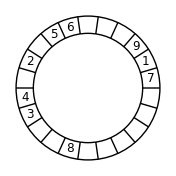

4 7 10 {1,2,0,4,3,0,0,6,5,0,0,0,0,9,0,7,0,0,0,0,0,8}

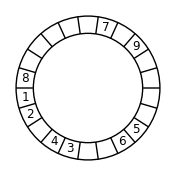

4 7 2 {1,8,0,0,0,0,0,0,0,9,0,0,0,0,5,6,7,0,4,3,0,2}

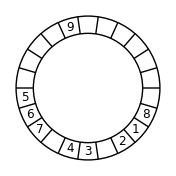

4 7 7 {1,9,0,0,3,0,0,7,0,0,6,0,0,0,4,0,2,0,8,0,0,5}

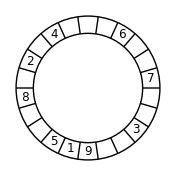

4 8 5 {1,2,0,3,4,0,7,6,5,0,0,0,0,9,0,0,0,0,0,0,0,8}

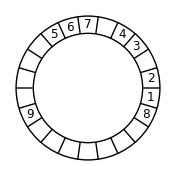

4 9 4 {1,4,0,0,0,5,7,6,0,0,3,0,0,8,0,0,0,0,0,9,0,2}

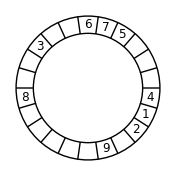

5 6 9 {1,5,0,0,0,0,8,0,9,0,0,0,0,0,6,0,0,3,4,0,2,7}

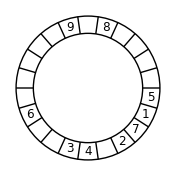

5 6 10 {1,7,0,0,0,0,6,0,8,0,0,3,4,0,2,0,5,0,0,0,0,9}

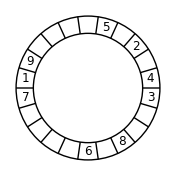

5 7 8 {1,5,0,0,8,0,2,0,4,0,0,0,6,0,0,7,0,0,3,0,0,9}

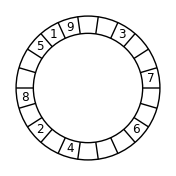

5 9 9 {1,2,0,3,0,0,5,0,0,0,7,8,0,0,0,0,0,6,0,9,0,4}

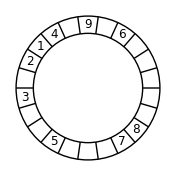

5 9 8 {1,4,0,0,0,5,7,6,0,0,3,0,0,8,0,0,0,0,0,9,0,2}

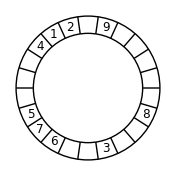

5 9 2 {1,5,0,0,8,0,2,0,4,0,0,0,6,0,0,7,0,0,3,0,0,9}

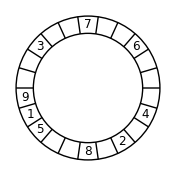

5 9 3 {1,9,0,0,5,0,6,0,0,3,4,0,2,0,8,0,0,0,0,0,0,7}

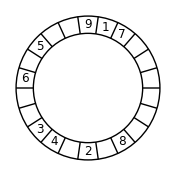

6 7 9 {1,2,0,6,0,0,0,0,0,8,0,0,9,0,0,0,7,5,0,3,0,4}

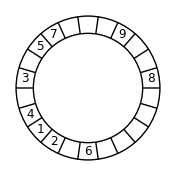

6 7 10 {1,4,0,0,0,5,7,0,0,0,9,0,0,8,0,0,6,0,0,3,0,2}

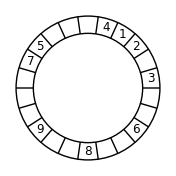

6 7 5 {1,7,0,0,0,0,6,0,8,0,0,3,4,0,2,0,5,0,0,0,0,9}

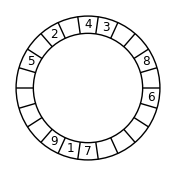

6 7 8 {1,8,0,0,0,0,0,7,0,9,0,0,0,0,5,6,0,0,3,4,0,2}

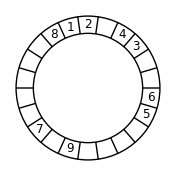

6 7 3 {1,9,0,0,3,0,0,7,0,0,6,0,0,0,4,0,2,0,8,0,0,5}

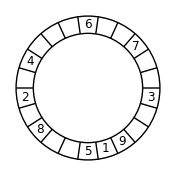

6 8 9 {1,7,0,0,0,0,0,0,8,0,0,3,4,0,2,0,5,6,0,0,0,9}

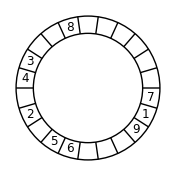

6 8 2 {1,9,0,0,0,0,5,0,2,0,4,3,0,0,8,0,6,0,0,0,0,7}

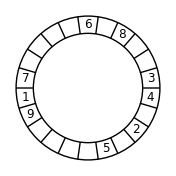

6 9 10 {1,4,0,0,0,5,7,6,0,0,3,0,0,8,0,0,0,0,0,9,0,2}

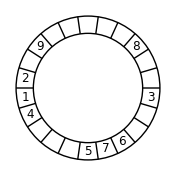

6 9 2 {1,4,0,9,0,6,0,0,0,0,0,8,7,0,0,0,5,0,0,3,0,2}

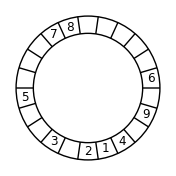

6 9 7 {1,7,0,0,0,0,6,0,8,0,0,3,4,0,2,0,5,0,0,0,0,9}

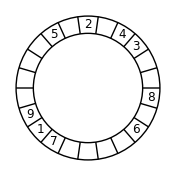

6 9 4 {1,9,0,0,0,6,5,0,2,0,4,3,0,0,8,0,0,0,0,0,0,7}

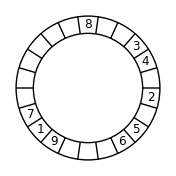

7 8 6 {1,8,0,0,0,0,0,7,0,9,0,0,0,0,5,6,0,0,3,4,0,2}

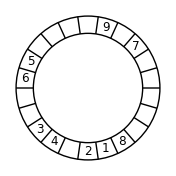

7 9 5 {1,4,0,0,0,5,0,0,8,0,9,0,0,0,0,7,6,0,0,3,0,2}

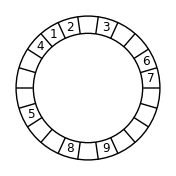

7 9 6 {1,9,0,0,3,0,0,7,0,0,6,0,0,0,4,0,2,0,8,0,0,5}

-Graphics-

8 9 6 {1,2,0,9,0,0,0,0,0,8,0,0,3,0,0,6,7,5,0,0,0,4}

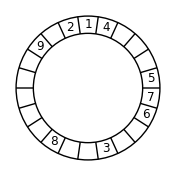

8 9 5 {1,5,0,0,8,0,2,0,4,0,0,0,6,0,0,7,0,0,3,0,0,9}

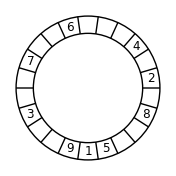

```mathematica
sizeq=9;
cir=22;
For[n=1,n≤sizeq-1,n++,
For[m=n+1,m≤sizeq,m++,
c=Table[
pn=Position[sols[[j]],n][[1,1]];
pm=Position[sols[[j]],m][[1,1]];
minus[pn,pm,cir],{j,1,Length[sols]}];
d=Select[unique[c],#≤cir/2&];
For[o=1,o≤Length[d],o++,
dd=d[[o]];
p=Position[c,dd][[1,1]];
s=sols[[p]];
Print[n," ",m," ",dd," ",s];Print[pic[s,cir,RandomInteger[{1,cir}]]]]]]
```

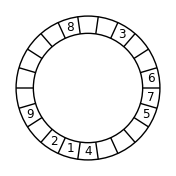

```mathematica
pic[{1,4,0,0,0,5,7,6,0,0,3,0,0,8,0,0,0,0,0,9,0,2},22,9]
```

1 2 4 {1,3,8,0,6,0,0,0,0,0,9,0,0,0,0,0,0,7,0,2,0,4,5}

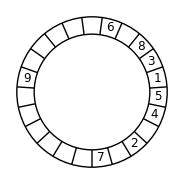

1 2 6 {1,5,0,0,0,0,6,0,0,8,0,0,3,0,0,9,0,2,0,4,0,0,7}

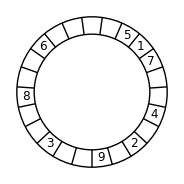

1 2 10 {1,9,0,0,0,0,5,6,0,0,3,4,0,2,0,8,0,0,0,0,0,0,7}

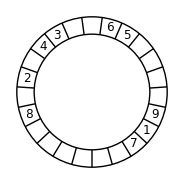

1 3 11 {1,5,0,0,0,0,6,0,0,8,0,0,3,0,0,9,0,2,0,4,0,0,7}

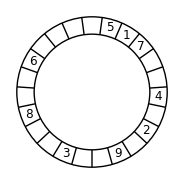

1 3 1 {1,5,4,0,2,0,7,0,0,0,0,0,0,9,0,0,0,0,0,6,0,8,3}

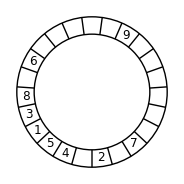

1 3 2 {1,6,0,0,0,0,0,9,0,0,0,0,0,0,7,0,2,0,4,5,0,3,8}

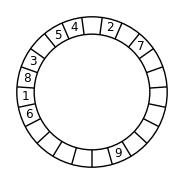

1 3 10 {1,7,0,0,0,0,0,0,8,0,2,0,4,3,0,0,6,5,0,0,0,0,9}

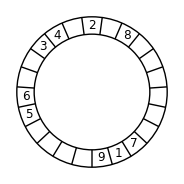

1 3 6 {1,7,0,0,0,0,0,0,9,0,0,0,0,0,6,0,8,3,0,5,4,0,2}

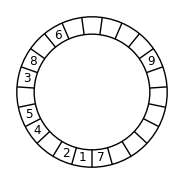

1 4 2 {1,3,8,0,6,0,0,0,0,0,9,0,0,0,0,0,0,7,0,2,0,4,5}

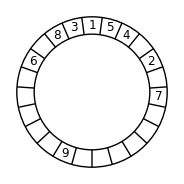

1 4 3 {1,7,0,0,0,0,0,0,9,0,0,0,0,0,6,0,8,3,0,5,4,0,2}

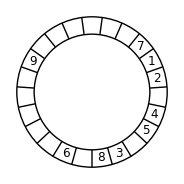

1 4 10 {1,7,0,6,0,0,0,0,5,8,0,0,0,4,0,0,0,9,0,0,3,0,2}

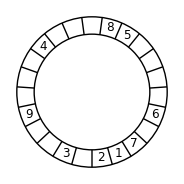

1 5 8 {1,2,0,3,0,0,9,0,0,0,4,0,0,0,8,5,0,0,0,0,6,0,7}

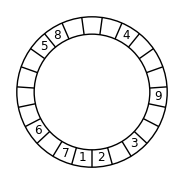

1 5 2 {1,2,0,7,0,0,0,0,0,0,9,0,0,0,0,0,6,0,8,3,0,5,4}

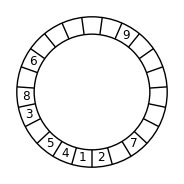

1 5 9 {1,6,0,0,0,0,0,7,0,9,0,0,0,0,5,0,2,0,4,3,0,0,8}

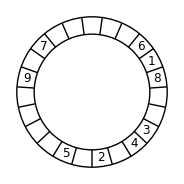

1 6 3 {1,2,0,3,0,0,9,0,0,0,4,0,0,0,8,5,0,0,0,0,6,0,7}

-Graphics-

1 6 4 {1,5,4,0,2,0,7,0,0,0,0,0,0,9,0,0,0,0,0,6,0,8,3}

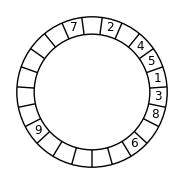

1 7 6 {1,3,8,0,6,0,0,0,0,0,9,0,0,0,0,0,0,7,0,2,0,4,5}

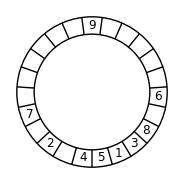

1 7 11 {1,4,0,0,0,5,0,0,0,0,9,0,7,0,0,0,6,0,0,3,8,0,2}

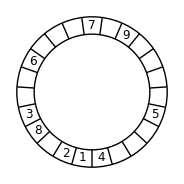

1 7 9 {1,6,0,0,0,0,0,9,0,0,0,0,0,0,7,0,2,0,4,5,0,3,8}

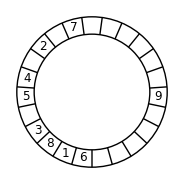

1 7 7 {1,8,0,0,3,4,0,2,0,5,0,0,0,0,9,0,7,0,0,0,0,0,6}

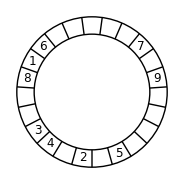

1 8 3 {1,4,0,0,0,5,0,0,0,0,9,0,7,0,0,0,6,0,0,3,8,0,2}

-Graphics-

1 8 2 {1,5,4,0,2,0,7,0,0,0,0,0,0,9,0,0,0,0,0,6,0,8,3}

-Graphics-

1 8 8 {1,9,0,0,0,0,5,6,0,0,3,4,0,2,0,8,0,0,0,0,0,0,7}

-Graphics-

1 9 1 {1,7,0,0,0,0,0,0,8,0,2,0,4,3,0,0,6,5,0,0,0,0,9}

-Graphics-

1 9 6 {1,7,0,6,0,0,0,0,5,8,0,0,0,4,0,0,0,9,0,0,3,0,2}

-Graphics-

1 9 9 {1,8,0,0,3,4,0,2,0,5,0,0,0,0,9,0,7,0,0,0,0,0,6}

-Graphics-

1 9 7 {1,8,3,0,5,4,0,2,0,7,0,0,0,0,0,0,9,0,0,0,0,0,6}

-Graphics-

2 4 9 {1,7,0,6,0,0,0,0,5,8,0,0,0,4,0,0,0,9,0,0,3,0,2}

-Graphics-

2 5 9 {1,2,0,3,0,0,9,0,0,0,4,0,0,0,8,5,0,0,0,0,6,0,7}

-Graphics-

2 5 6 {1,2,0,8,3,0,0,6,0,0,0,7,0,9,0,0,0,0,5,0,0,0,4}

-Graphics-

2 5 4 {1,4,0,0,3,8,0,6,0,0,0,0,0,9,0,0,0,0,5,0,7,0,2}

-Graphics-

2 5 2 {1,6,0,0,0,0,0,7,0,9,0,0,0,0,5,0,2,0,4,3,0,0,8}

-Graphics-

2 6 11 {1,5,0,0,0,0,6,0,0,8,0,0,3,0,0,9,0,2,0,4,0,0,7}

-Graphics-

2 7 10 {1,4,0,0,0,5,0,0,0,0,9,0,7,0,0,0,6,0,0,3,8,0,2}

-Graphics-

2 7 5 {1,7,0,0,4,0,2,0,9,0,0,3,0,0,8,0,0,6,0,0,0,0,5}

-Graphics-

2 8 8 {1,5,0,0,0,0,6,0,0,8,0,0,3,0,0,9,0,2,0,4,0,0,7}

-Graphics-

2 9 2 {1,5,0,0,0,0,6,0,0,8,0,0,3,0,0,9,0,2,0,4,0,0,7}

-Graphics-

2 9 7 {1,6,0,0,0,0,0,7,0,9,0,0,0,0,5,0,2,0,4,3,0,0,8}

-Graphics-

2 9 5 {1,7,0,6,0,0,0,0,5,8,0,0,0,4,0,0,0,9,0,0,3,0,2}

-Graphics-

3 4 5 {1,2,0,8,3,0,0,6,0,0,0,7,0,9,0,0,0,0,5,0,0,0,4}

-Graphics-

3 5 5 {1,6,0,0,0,0,0,7,0,9,0,0,0,0,5,0,2,0,4,3,0,0,8}

-Graphics-

3 5 4 {1,9,0,0,0,0,5,6,0,0,3,4,0,2,0,8,0,0,0,0,0,0,7}

-Graphics-

3 6 5 {1,8,0,0,3,4,0,2,0,5,0,0,0,0,9,0,7,0,0,0,0,0,6}

-Graphics-

3 7 10 {1,7,0,0,4,0,2,0,9,0,0,3,0,0,8,0,0,6,0,0,0,0,5}

-Graphics-

3 8 5 {1,7,0,0,0,0,0,0,8,0,2,0,4,3,0,0,6,5,0,0,0,0,9}

-Graphics-

3 8 11 {1,7,0,6,0,0,0,0,5,8,0,0,0,4,0,0,0,9,0,0,3,0,2}

-Graphics-

3 9 10 {1,6,0,0,0,0,0,7,0,9,0,0,0,0,5,0,2,0,4,3,0,0,8}

-Graphics-

4 5 6 {1,4,0,0,3,8,0,6,0,0,0,0,0,9,0,0,0,0,5,0,7,0,2}

-Graphics-

4 6 8 {1,4,0,0,0,5,0,0,0,0,9,0,7,0,0,0,6,0,0,3,8,0,2}

-Graphics-

4 6 9 {1,7,0,0,4,0,0,0,9,0,0,0,8,0,0,0,0,5,6,0,3,0,2}

-Graphics-

4 6 4 {1,9,0,0,0,0,5,6,0,0,3,4,0,2,0,8,0,0,0,0,0,0,7}

-Graphics-

4 8 10 {1,5,0,0,0,0,6,0,0,8,0,0,3,0,0,9,0,2,0,4,0,0,7}

-Graphics-

4 9 10 {1,9,0,0,0,0,5,6,0,0,3,4,0,2,0,8,0,0,0,0,0,0,7}

-Graphics-

5 6 10 {1,8,0,0,3,4,0,2,0,5,0,0,0,0,9,0,7,0,0,0,0,0,6}

-Graphics-

5 8 10 {1,2,0,7,0,5,0,0,0,0,9,0,0,0,0,0,6,0,8,3,0,0,4}

-Graphics-

5 8 9 {1,7,0,0,0,0,0,0,8,0,2,0,4,3,0,0,6,5,0,0,0,0,9}

-Graphics-

6 7 4 {1,4,0,0,0,5,0,0,0,0,9,0,7,0,0,0,6,0,0,3,8,0,2}

-Graphics-

6 7 7 {1,5,0,0,0,0,6,0,0,8,0,0,3,0,0,9,0,2,0,4,0,0,7}

-Graphics-

6 7 2 {1,7,0,6,0,0,0,0,5,8,0,0,0,4,0,0,0,9,0,0,3,0,2}

-Graphics-

6 7 8 {1,9,0,0,0,0,5,6,0,0,3,4,0,2,0,8,0,0,0,0,0,0,7}

-Graphics-

6 8 10 {1,2,0,3,0,0,5,8,0,0,0,4,0,0,0,9,0,6,0,0,0,0,7}

-Graphics-

6 8 4 {1,2,0,8,3,0,0,6,0,0,0,7,0,9,0,0,0,0,5,0,0,0,4}

-Graphics-

6 8 8 {1,7,0,0,0,0,0,0,8,0,2,0,4,3,0,0,6,5,0,0,0,0,9}

-Graphics-

6 8 3 {1,7,0,0,4,0,2,0,9,0,0,3,0,0,8,0,0,6,0,0,0,0,5}

-Graphics-

6 9 8 {1,8,0,0,3,4,0,2,0,5,0,0,0,0,9,0,7,0,0,0,0,0,6}

-Graphics-

7 8 10 {1,7,0,0,4,0,2,0,9,0,0,3,0,0,8,0,0,6,0,0,0,0,5}

-Graphics-

7 8 7 {1,9,0,0,0,0,5,6,0,0,3,4,0,2,0,8,0,0,0,0,0,0,7}

-Graphics-

8 9 9 {1,7,0,0,0,0,0,0,8,0,2,0,4,3,0,0,6,5,0,0,0,0,9}

-Graphics-

8 9 6 {1,7,0,0,4,0,2,0,9,0,0,3,0,0,8,0,0,6,0,0,0,0,5}

-Graphics-

```mathematica
sizeq=9;
cir=23;
For[n=1,n≤sizeq-1,n++,
For[m=n+1,m≤sizeq,m++,
c=Table[
pn=Position[sols[[j]],n][[1,1]];
pm=Position[sols[[j]],m][[1,1]];
minus[pn,pm,cir],{j,1,Length[sols]}];
d=Select[unique[c],#≤cir/2&];
For[o=1,o≤Length[d],o++,
dd=d[[o]];
p=Position[c,dd][[1,1]];
s=sols[[p]];
Print[n," ",m," ",dd," ",s];Print[pic[s,cir,RandomInteger[{1,cir}]]]]]]
```

```mathematica
f[9,25]
```

-Graphics-

-Graphics-

```mathematica
f[9,19]
```

```mathematica
sizeq=9;
cir=19;
For[n=1,n≤sizeq-1,n++,
For[m=n+1,m≤sizeq,m++,
c=Table[
pn=Position[sols[[j]],n][[1,1]];
pm=Position[sols[[j]],m][[1,1]];
minus[pn,pm,cir],{j,1,Length[sols]}];
d=Select[unique[c],#≤cir/2&];
For[o=1,o≤Length[d],o++,
dd=d[[o]];
p=Position[c,dd][[1,1]];
s=sols[[p]];
Print[n," ",m," ",dd," ",s];Print[pic[s,cir,RandomInteger[{1,cir}]]]]]]
```

1 2 5 {1,6,0,0,0,0,0,7,0,0,9,0,5,0,2,0,4,3,8}

-Graphics-

1 7 5 {1,6,5,0,0,0,0,8,0,0,0,9,0,0,7,4,2,0,3}

-Graphics-

1 8 2 {1,2,0,3,0,4,5,0,0,9,0,6,0,0,0,0,0,8,7}

-Graphics-

1 9 7 {1,2,4,3,0,0,6,0,0,0,0,8,9,0,0,0,0,5,7}

-Graphics-

2 3 4 {1,2,0,4,7,0,0,6,0,0,0,8,0,9,0,0,3,0,5}

-Graphics-

2 4 9 {1,2,0,3,0,6,5,8,0,0,0,4,0,0,0,9,0,0,7}

-Graphics-

2 5 9 {1,7,0,2,0,6,0,0,3,4,0,8,0,5,0,0,0,0,9}

-Graphics-

3 5 6 {1,7,2,0,4,3,0,0,6,0,0,0,0,8,9,0,0,0,5}

-Graphics-

3 6 4 {1,2,0,3,0,4,5,0,0,9,0,8,7,0,0,0,0,0,6}

-Graphics-

3 8 2 {1,3,0,0,6,0,0,7,0,0,9,0,0,0,4,5,0,2,8}

-Graphics-

4 6 8 {1,5,0,0,0,0,6,7,0,0,9,0,2,0,4,3,0,0,8}

-Graphics-

4 8 1 {1,7,0,0,0,6,0,0,8,4,0,2,0,5,0,0,3,0,9}

-Graphics-

4 9 1 {1,6,0,0,0,0,0,7,0,0,9,4,0,0,3,5,0,2,8}

-Graphics-

5 7 3 {1,6,0,0,0,9,0,7,0,0,5,0,2,0,4,3,0,0,8}

-Graphics-

5 9 6 {1,8,0,0,0,4,0,0,7,9,2,0,3,0,0,5,0,0,6}

-Graphics-

6 7 8 {1,2,0,4,3,0,5,6,0,0,0,8,0,9,0,0,0,0,7}

-Graphics-

6 9 7 {1,8,3,0,0,4,0,5,0,2,0,9,7,0,0,0,0,0,6}

-Graphics-

7 8 3 {1,9,0,0,4,0,0,0,8,0,6,7,0,5,0,0,3,0,2}

-Graphics-

```mathematica
f[9,20]
```

```mathematica
sizeq=9;
cir=20;
For[n=1,n≤sizeq-1,n++,
For[m=n+1,m≤sizeq,m++,
c=Table[
pn=Position[sols[[j]],n][[1,1]];
pm=Position[sols[[j]],m][[1,1]];
minus[pn,pm,cir],{j,1,Length[sols]}];
d=Select[unique[c],#≤cir/2&];
For[o=1,o≤Length[d],o++,
dd=d[[o]];
p=Position[c,dd][[1,1]];
s=sols[[p]];
Print[n," ",m," ",dd," ",s];Print[pic[s,cir,RandomInteger[{1,cir}]]]]]]
```

1 2 5 {1,5,0,0,0,8,9,0,0,0,0,0,0,7,0,2,3,4,0,6}

-Graphics-

1 2 7 {1,6,0,0,0,0,0,8,7,0,3,4,0,2,0,5,0,0,0,9}

-Graphics-

1 2 4 {1,7,6,0,0,0,0,0,8,9,0,0,0,0,5,0,2,0,4,3}

-Graphics-

1 4 2 {1,7,6,0,0,0,0,0,8,9,0,0,0,0,5,0,2,0,4,3}

-Graphics-

1 5 8 {1,9,0,0,8,0,0,3,0,0,6,0,5,0,0,0,4,7,0,2}

-Graphics-

1 6 4 {1,4,3,0,0,5,0,0,0,7,9,0,0,0,0,0,6,8,0,2}

-Graphics-

1 8 6 {1,9,3,0,0,5,6,0,0,0,4,0,2,0,8,0,0,0,0,7}

-Graphics-

2 3 8 {1,2,0,7,4,0,0,0,5,0,6,0,0,3,0,0,8,0,0,9}

-Graphics-

2 4 1 {1,5,0,0,0,0,9,0,0,8,0,0,3,0,0,6,4,2,0,7}

-Graphics-

2 4 9 {1,6,0,0,0,0,9,8,0,0,4,0,0,0,7,5,0,3,0,2}

-Graphics-

2 7 8 {1,6,2,0,3,0,0,8,0,0,0,9,0,0,7,4,0,0,0,5}

-Graphics-

2 8 9 {1,2,0,9,3,0,0,7,4,0,0,0,8,0,6,0,0,0,0,5}

-Graphics-

2 8 1 {1,8,2,0,5,4,0,0,0,7,0,0,0,9,0,0,3,0,0,6}

-Graphics-

2 9 4 {1,4,0,2,0,5,0,0,3,0,7,8,0,0,0,0,0,6,0,9}

-Graphics-

2 9 5 {1,4,0,6,0,5,0,0,0,8,7,0,0,0,9,0,0,3,0,2}

-Graphics-

2 9 3 {1,7,6,0,0,0,0,0,8,0,0,9,4,0,2,0,5,0,0,3}

-Graphics-

3 4 2 {1,6,5,0,0,0,0,8,0,0,0,9,0,0,7,4,0,3,0,2}

-Graphics-

3 5 4 {1,4,0,0,0,5,6,0,0,3,9,0,7,0,0,0,0,8,0,2}

-Graphics-

3 6 1 {1,5,0,0,0,0,9,0,0,8,0,0,0,7,0,6,3,4,0,2}

-Graphics-

3 6 8 {1,5,0,3,0,0,9,0,0,8,0,0,0,0,0,6,7,2,0,4}

-Graphics-

3 6 5 {1,7,2,0,4,0,0,0,8,0,0,9,0,0,6,0,5,0,0,3}

-Graphics-

3 8 6 {1,4,0,2,7,6,0,0,0,0,0,8,0,0,9,0,0,3,0,5}

-Graphics-

4 6 7 {1,3,0,0,5,4,0,0,0,9,0,0,7,0,0,0,0,8,6,2}

-Graphics-

4 6 3 {1,6,0,0,4,0,0,3,7,0,2,0,8,0,0,5,0,0,0,9}

-Graphics-

4 7 2 {1,9,0,0,8,0,0,3,0,0,6,0,2,0,7,0,4,0,0,5}

-Graphics-

4 8 9 {1,4,3,0,7,6,0,0,0,0,0,9,8,0,0,0,0,5,0,2}

-Graphics-

4 8 7 {1,5,0,0,0,0,9,0,0,8,0,0,3,0,0,6,4,2,0,7}

-Graphics-

4 8 3 {1,6,0,0,0,0,9,8,0,0,4,0,0,0,7,5,0,3,0,2}

-Graphics-

4 8 1 {1,9,0,0,0,0,6,0,0,8,4,0,2,0,5,0,0,3,0,7}

-Graphics-

4 9 2 {1,4,0,2,0,5,0,0,3,0,7,8,0,0,0,0,0,6,0,9}

-Graphics-

5 7 4 {1,2,0,8,6,0,0,0,0,0,9,7,0,0,0,5,0,0,3,4}

-Graphics-

5 9 8 {1,6,2,0,3,0,0,8,0,0,0,9,0,0,7,4,0,0,0,5}

-Graphics-

6 7 5 {1,2,0,4,0,0,0,8,7,0,3,0,0,6,0,5,0,0,0,9}

-Graphics-

6 7 9 {1,4,0,2,0,5,0,0,0,0,7,0,0,8,9,0,0,3,0,6}

-Graphics-

6 7 8 {1,6,0,0,0,0,9,8,0,0,3,0,0,7,0,5,0,4,0,2}

-Graphics-

6 8 7 {1,2,0,5,0,0,0,0,8,9,0,0,0,0,0,6,7,0,3,4}

-Graphics-

6 8 3 {1,7,0,3,0,0,5,0,2,0,4,8,0,0,6,0,0,0,0,9}

-Graphics-

6 9 4 {1,2,0,8,0,0,0,0,7,0,9,3,0,0,6,5,0,0,0,4}

-Graphics-

7 8 6 {1,6,0,0,0,0,9,8,0,0,3,0,0,7,0,5,0,4,0,2}

-Graphics-

8 9 6 {1,4,3,0,0,6,0,0,0,7,0,9,0,0,0,0,5,8,0,2}

-Graphics-

```mathematica
pic[{1,5,0,0,0,8,9,0,0,0,0,0,0,7,0,2,3,4,0,6},20,18]
```

-Graphics-

```mathematica
f[9,21]
```

```mathematica
sizeq=9;
cir=21;
For[n=1,n≤sizeq-1,n++,
For[m=n+1,m≤sizeq,m++,
c=Table[
pn=Position[sols[[j]],n][[1,1]];
pm=Position[sols[[j]],m][[1,1]];
minus[pn,pm,cir],{j,1,Length[sols]}];
d=Select[unique[c],#≤cir/2&];
For[o=1,o≤Length[d],o++,
dd=d[[o]];
p=Position[c,dd][[1,1]];
s=sols[[p]];
Print[n," ",m," ",dd," ",s];Print[pic[s,cir,RandomInteger[{1,cir}]]]]]]
```

1 2 2 {1,6,0,0,0,0,0,9,0,0,0,0,5,0,7,0,4,3,0,2,8}

-Graphics-

1 3 6 {1,2,0,9,4,0,0,0,7,0,0,0,8,0,0,3,0,0,6,0,5}

-Graphics-

1 4 8 {1,2,0,3,0,0,6,0,0,8,0,0,9,4,0,0,0,5,0,0,7}

-Graphics-

1 4 9 {1,6,0,0,0,0,0,7,8,0,0,3,4,0,2,0,5,0,0,0,9}

-Graphics-

1 5 4 {1,2,0,3,0,0,6,0,0,8,0,0,9,4,0,0,0,5,0,0,7}

-Graphics-

1 6 3 {1,2,0,9,4,0,0,0,7,0,0,0,8,0,0,3,0,0,6,0,5}

-Graphics-

1 7 4 {1,2,0,5,0,0,0,0,8,0,9,0,0,0,0,0,6,7,0,3,4}

-Graphics-

1 7 6 {1,2,0,5,0,0,0,0,8,0,9,0,0,0,0,7,6,0,0,3,4}

-Graphics-

1 7 9 {1,4,0,0,0,5,0,0,0,0,9,0,7,0,0,0,6,0,8,3,2}

-Graphics-

1 8 5 {1,2,0,3,0,0,6,0,5,0,0,0,9,7,0,0,8,0,0,0,4}

-Graphics-

1 8 3 {1,4,0,0,0,5,0,0,0,0,9,0,7,0,0,0,6,0,8,3,2}

-Graphics-

1 9 6 {1,2,0,3,4,0,6,0,7,0,0,0,8,0,0,9,0,0,0,0,5}

-Graphics-

1 9 3 {1,5,0,6,0,0,3,0,0,8,0,0,0,7,0,0,0,4,9,0,2}

-Graphics-

1 9 5 {1,8,0,0,3,4,0,2,0,5,0,0,0,0,7,0,9,0,0,0,6}

-Graphics-

1 9 7 {1,8,2,0,3,4,0,7,0,5,0,0,0,0,9,0,0,0,0,0,6}

-Graphics-

2 3 5 {1,2,0,4,0,0,0,7,9,0,0,0,5,0,6,0,0,3,0,0,8}

-Graphics-

2 3 7 {1,2,0,9,4,0,0,0,7,0,0,0,8,0,0,3,0,0,6,0,5}

-Graphics-

2 3 1 {1,4,0,0,0,5,0,0,0,0,9,0,7,0,0,0,6,0,8,3,2}

-Graphics-

2 3 10 {1,9,0,0,0,5,0,6,0,0,3,0,0,8,7,0,0,0,4,0,2}

-Graphics-

2 4 9 {1,2,0,3,0,0,6,0,0,8,0,0,9,4,0,0,0,5,0,0,7}

-Graphics-

2 5 5 {1,2,0,3,0,0,6,0,0,8,0,0,9,4,0,0,0,5,0,0,7}

-Graphics-

2 5 10 {1,2,0,4,0,0,0,7,9,0,0,0,5,0,6,0,0,3,0,0,8}

-Graphics-

2 6 3 {1,8,2,0,3,4,0,7,0,5,0,0,0,0,9,0,0,0,0,0,6}

-Graphics-

2 7 9 {1,2,0,3,0,0,6,0,5,0,0,0,9,7,0,0,8,0,0,0,4}

-Graphics-

2 7 8 {1,4,0,0,0,5,0,0,0,0,9,0,7,0,0,0,6,0,8,3,2}

-Graphics-

2 8 8 {1,7,0,0,5,0,0,0,4,9,0,0,8,0,0,6,0,0,3,0,2}

-Graphics-

2 8 1 {1,8,2,0,3,4,0,7,0,5,0,0,0,0,9,0,0,0,0,0,6}

-Graphics-

3 4 4 {1,2,0,3,0,0,6,0,5,0,0,0,9,7,0,0,8,0,0,0,4}

-Graphics-

3 4 8 {1,2,0,4,0,0,0,7,8,0,0,3,0,0,6,0,5,0,0,0,9}

-Graphics-

3 4 3 {1,2,3,8,0,6,0,0,0,7,0,9,0,0,0,0,5,0,0,0,4}

-Graphics-

3 4 7 {1,8,0,0,3,0,0,6,0,5,0,0,0,9,7,0,0,0,4,0,2}

-Graphics-

3 5 4 {1,2,0,3,4,0,6,0,7,0,0,0,8,0,0,9,0,0,0,0,5}

-Graphics-

3 6 10 {1,6,0,0,0,0,0,7,8,0,0,3,4,0,2,0,5,0,0,0,9}

-Graphics-

3 7 2 {1,2,0,5,0,0,0,0,8,0,9,0,0,0,0,0,6,7,0,3,4}

-Graphics-

3 7 5 {1,5,0,0,0,0,9,0,0,8,0,0,0,7,0,6,0,4,3,0,2}

-Graphics-

3 7 3 {1,6,0,0,0,0,0,9,0,0,0,0,5,0,7,0,4,3,0,2,8}

-Graphics-

3 8 8 {1,2,0,3,0,0,6,0,5,0,0,0,9,7,0,0,8,0,0,0,4}

-Graphics-

3 8 1 {1,4,0,0,0,5,0,0,0,0,9,0,7,0,0,0,6,0,8,3,2}

-Graphics-

3 8 6 {1,7,0,0,5,0,0,0,4,9,0,0,8,0,0,6,0,0,3,0,2}

-Graphics-

4 5 8 {1,2,0,4,0,0,0,7,8,0,0,3,0,0,6,0,5,0,0,0,9}

-Graphics-

4 7 3 {1,2,0,5,0,0,0,0,8,0,9,0,0,0,0,0,6,7,0,3,4}

-Graphics-

4 7 10 {1,4,0,0,0,5,0,0,0,0,9,0,7,0,0,0,6,0,8,3,2}

-Graphics-

4 7 2 {1,6,0,0,0,0,0,9,0,0,0,0,5,0,7,0,4,3,0,2,8}

-Graphics-

4 8 5 {1,9,0,0,0,5,0,6,0,0,3,0,0,8,7,0,0,0,4,0,2}

-Graphics-

4 9 4 {1,2,0,4,0,0,0,7,8,0,0,3,0,0,6,0,5,0,0,0,9}

-Graphics-

4 9 5 {1,8,0,0,3,0,0,6,0,5,0,0,0,9,7,0,0,0,4,0,2}

-Graphics-

5 6 7 {1,5,0,0,0,0,9,0,0,8,0,0,0,7,0,6,0,4,3,0,2}

-Graphics-

5 6 6 {1,9,0,0,0,5,0,2,0,4,3,0,0,8,7,0,0,0,0,0,6}

-Graphics-

5 7 3 {1,7,0,0,5,0,0,0,4,9,0,0,8,0,0,6,0,0,3,0,2}

-Graphics-

5 7 2 {1,8,2,0,3,4,0,7,0,5,0,0,0,0,9,0,0,0,0,0,6}

-Graphics-

5 8 4 {1,7,0,0,0,0,0,0,9,8,0,0,0,5,0,6,0,4,3,0,2}

-Graphics-

6 7 10 {1,2,0,9,4,0,0,0,7,0,0,0,8,0,0,3,0,0,6,0,5}

-Graphics-

6 7 4 {1,4,0,0,0,5,0,0,0,0,9,0,7,0,0,0,6,0,8,3,2}

-Graphics-

6 7 2 {1,5,0,0,0,0,9,0,0,8,0,0,0,7,0,6,0,4,3,0,2}

-Graphics-

6 7 8 {1,6,0,0,0,0,0,9,0,0,0,0,5,0,7,0,4,3,0,2,8}

-Graphics-

6 8 10 {1,4,0,0,0,8,0,0,7,9,0,0,0,5,0,6,0,0,3,0,2}

-Graphics-

6 8 3 {1,7,0,0,5,0,0,0,4,9,0,0,8,0,0,6,0,0,3,0,2}

-Graphics-

6 8 7 {1,9,0,0,0,5,0,2,0,4,3,0,0,8,7,0,0,0,0,0,6}

-Graphics-

6 9 9 {1,5,0,0,0,0,9,0,0,8,0,0,0,7,0,6,0,4,3,0,2}

-Graphics-

6 9 2 {1,6,0,0,0,0,0,7,8,0,0,3,4,0,2,0,5,0,0,0,9}

-Graphics-

6 9 4 {1,8,0,0,3,4,0,2,0,5,0,0,0,0,7,0,9,0,0,0,6}

-Graphics-

7 8 9 {1,2,0,5,0,0,0,0,8,0,9,0,0,0,0,0,6,7,0,3,4}

-Graphics-

7 8 7 {1,2,0,5,0,0,0,0,8,0,9,0,0,0,0,7,6,0,0,3,4}

-Graphics-

7 8 3 {1,4,0,0,0,8,0,0,7,9,0,0,0,5,0,6,0,0,3,0,2}

-Graphics-

7 8 10 {1,7,0,0,5,0,0,0,4,9,0,0,8,0,0,6,0,0,3,0,2}

-Graphics-

8 9 4 {1,2,0,3,0,0,6,0,5,0,0,0,9,7,0,0,8,0,0,0,4}

-Graphics-

8 9 1 {1,7,0,0,0,0,0,0,9,8,0,0,0,5,0,6,0,4,3,0,2}

-Graphics-

8 9 6 {1,8,0,0,3,4,0,2,0,5,0,0,0,0,7,0,9,0,0,0,6}

-Graphics-